```mathematica
x1={10.080,14.369,18.748,23.060,27.048,31.323,35.598,39.880,44.302,48.886,53.240,57.477}
Upp1={32.0,27.4,24.2,20.0,17.6,16.0,14.8,13.4,12.4,11.4,10.2,9.28}
```

{{10.08,32.},{14.369,27.2},{18.748,24.4},{23.06,20.},{27.048,17.6},{31.323,16.},{35.598,14.8},{39.88,13.4},{44.302,12.4},{48.886,11.4},{53.24,10.2},{57.477,9.28}}

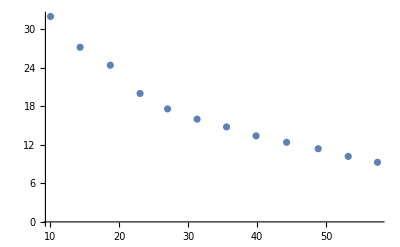

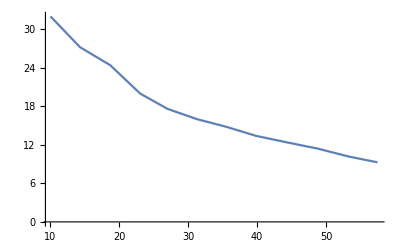

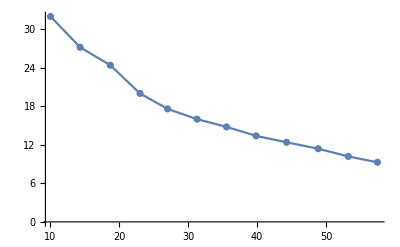

```mathematica
data1=Table[{x1[[i]],Upp1[[i]]},{i,1,12}]
grp11=ListPlot[data1]
grp12=ListLinePlot[data1]
Show[grp11,grp12]
```

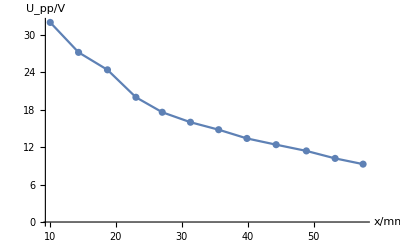

```mathematica
Show[%18,AxesLabel->{HoldForm[x/mm],HoldForm[U_pp/V]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

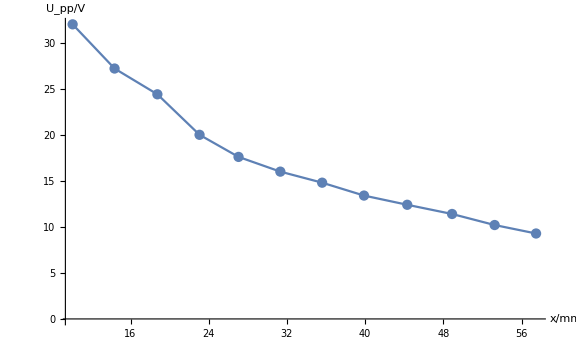

```mathematica
Show[%19,ImageSize->Large]
```

{10.05,14.321,18.721,23.079,27.062,31.316,35.522,39.878,44.312,48.871,53.158,57.462}

{32.2,27.4,24.4,20.2,17.4,15.9,14.8,13.3,12.4,11.3,10.1,9.28}

{{10.05,32.2},{14.321,27.4},{18.721,24.4},{23.079,20.2},{27.062,17.4},{31.316,15.9},{35.522,14.8},{39.878,13.3},{44.312,12.4},{48.871,11.3},{53.158,10.1},{57.462,9.28}}

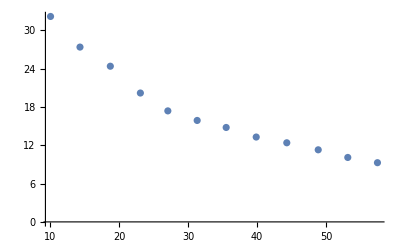

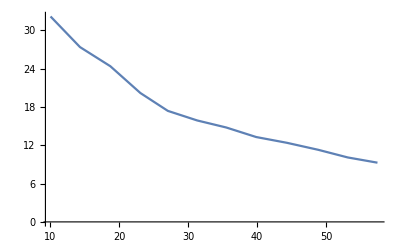

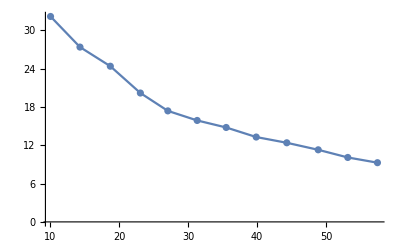

```mathematica
x2={10.050,14.321,18.721,23.079,27.062,31.316,35.522,39.878,44.312,48.871,53.158,57.462}
Upp2={32.2,27.4,24.4,20.2,17.4,15.9,14.8,13.3,12.4,11.3,10.1,9.28}
data2=Table[{x2[[i]],Upp2[[i]]},{i,1,12}]
grp21=ListPlot[data2]
grp22=ListLinePlot[data2]
Show[grp21,grp22]
```

{17.251,26.021,34.92,43.602,52.201,60.81,69.52,77.881,86.431,94.982,103.4,111.99}

{{1,17.251},{2,26.021},{3,34.92},{4,43.602},{5,52.201},{6,60.81},{7,69.52},{8,77.881},{9,86.431},{10,94.982},{11,103.4},{12,111.99}}

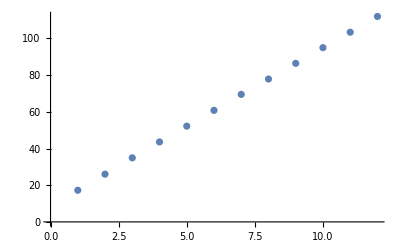

```mathematica
x3={17.251,26.021,34.920,43.602,52.201,60.810,69.520,77.881,86.431,94.982,103.400,111.990}
data3=Table[{i,x3[[i]]},{i,1,12}]
grp31=ListPlot[data3]
```

```mathematica
lf32=Fit[data3,{1,x},x]
```

9.03403+8.59744 x

```mathematica
Needs["LinearRegression`"]
Regress[data3,{1,x},x,RegressionReport->{RSquared}]
```

{RSquared→0.999954}

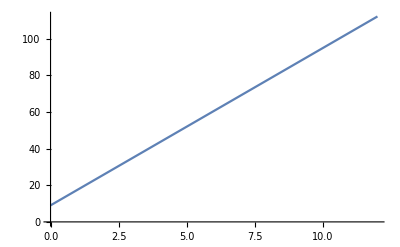

```mathematica
Plot[lf32,{x,0,12}]
```

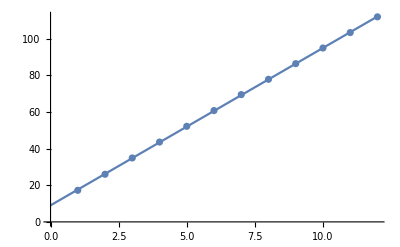

```mathematica
Show[%,grp31]
```

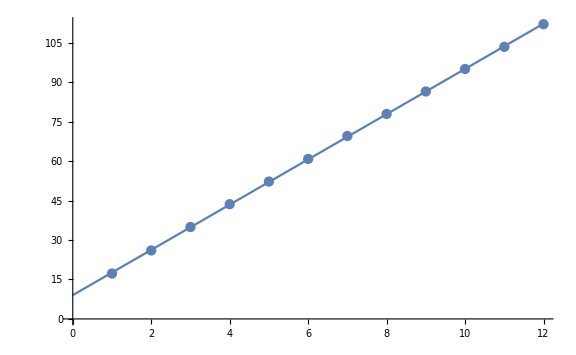

```mathematica
Show[%34,ImageSize->Large]
```

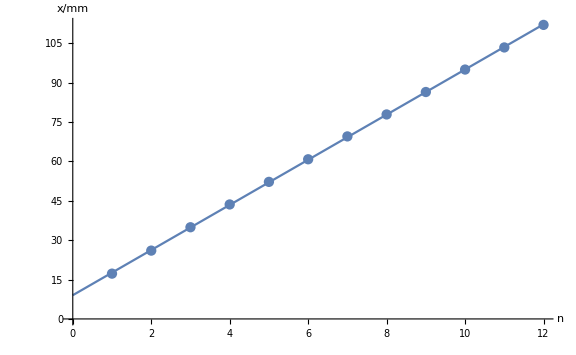

```mathematica
Show[%35,AxesLabel->{HoldForm[n],HoldForm[x/mm]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

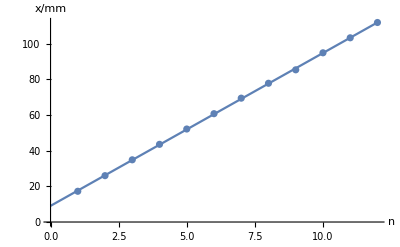

```mathematica
Show[%14,AxesLabel->{HoldForm[n],HoldForm[x/mm]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

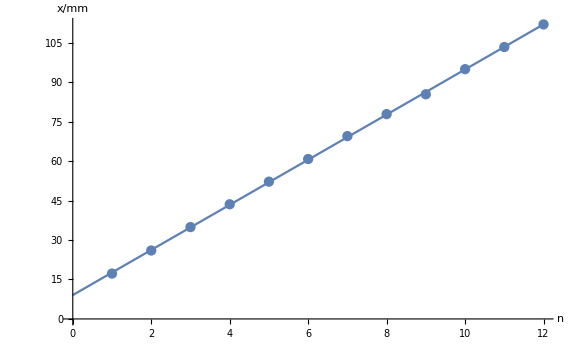

```mathematica
Show[%15,ImageSize->Large]
```

{17.15,25.97,34.845,43.526,52.105,60.775,69.472,77.79,86.3,94.865,103.245,111.975}

{{1,17.15},{2,25.97},{3,34.845},{4,43.526},{5,52.105},{6,60.775},{7,69.472},{8,77.79},{9,86.3},{10,94.865},{11,103.245},{12,111.975}}

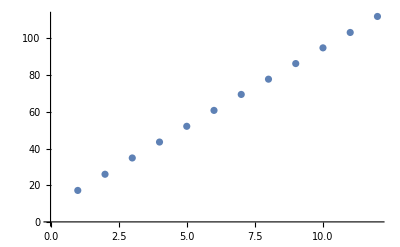

```mathematica
x4={17.150,25.970,34.845,43.526,52.105,60.775,69.472,77.790,86.300,94.865,103.245,111.975}
data4=Table[{i,x4[[i]]},{i,1,12}]
grp41=ListPlot[data4]
```

```mathematica
lf42=Fit[data4,{1,x},x]
```

```mathematica
8.96410606060607+8.595496503496502 x
```

```mathematica
Regress[data4,{1,x},x,RegressionReport->{RSquared}]
```

{RSquared→0.999949}

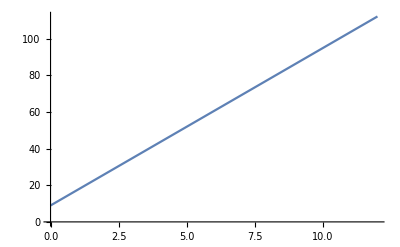

```mathematica
Plot[lf42,{x,0,12}]
```

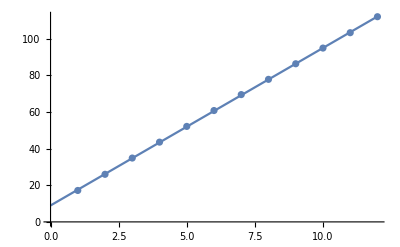

```mathematica
Show[%,grp41]
```

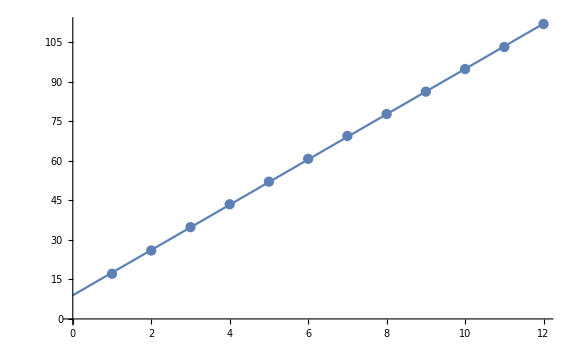

```mathematica
Show[%38,ImageSize->Large]
```

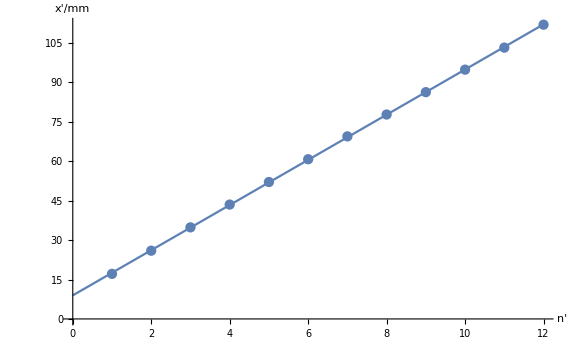

```mathematica
Show[%39,AxesLabel->{HoldForm[n'],HoldForm[x'/mm]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

{33.402,34.128,34.862,35.612,36.355,37.101,37.842,38.574,39.308,40.048,40.79,41.526}

{{1,33.402},{2,34.128},{3,34.862},{4,35.612},{5,36.355},{6,37.101},{7,37.842},{8,38.574},{9,39.308},{10,40.048},{11,40.79},{12,41.526}}

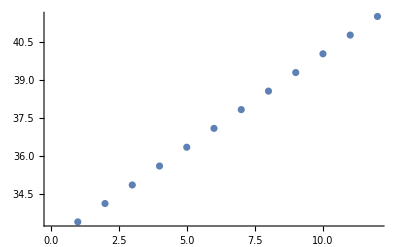

```mathematica
x5={33.402,34.128,34.862,35.612,36.355,37.101,37.842,38.574,39.308,40.048,40.790,41.526}
data5=Table[{i,x5[[i]]},{i,1,12}]
grp51=ListPlot[data5]
```

```mathematica
lf52=Fit[data5,{1,x},x]
```

32.6555+0.739517 x

```mathematica
Regress[data5,{1,x},x,RegressionReport->{RSquared}]
```

{RSquared→0.999994}

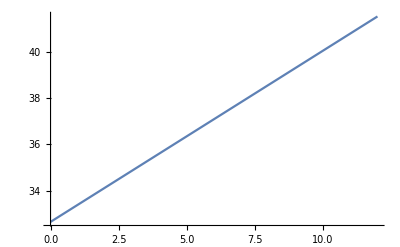

```mathematica
Plot[lf52,{x,0,12}]
```

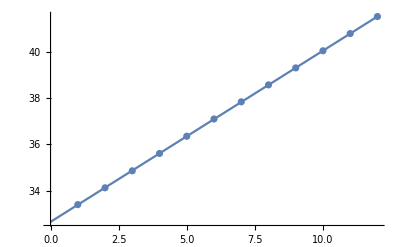

```mathematica
Show[%,grp51]
```

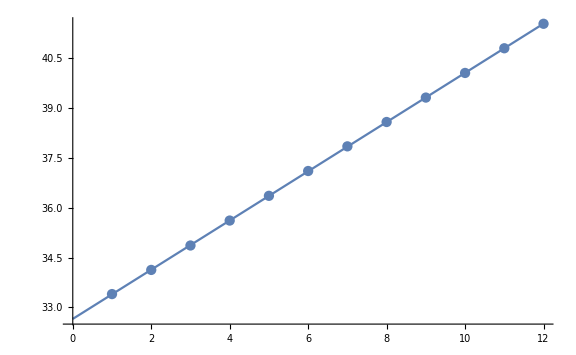

```mathematica
Show[%51,ImageSize->Large]
```

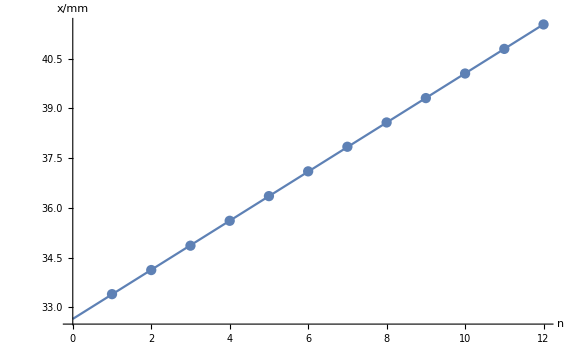

```mathematica
Show[%52,AxesLabel->{HoldForm[n],HoldForm[x/mm]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```